```mathematica
PGEnsemble=Import[FileNameJoin[{NotebookDirectory[],"PGEnsembleData.csv"}],"CSV"];
PGData =Import[FileNameJoin[{NotebookDirectory[],"PGData.csv"}],"CSV"];
PGLowess = Import[FileNameJoin[{NotebookDirectory[],"PGEnsembleLowess.csv"}],"CSV"];
```

```mathematica
PGEnsemble[[All,1]]=PGEnsemble[[All,1]]/(1000*3600);
PGLowess[[All,1]] = PGLowess[[All,1]]/(1000*3600);
```

```mathematica
PGEnsembleFit=NonlinearModelFit[PGEnsemble,plat+(y0-plat)*Exp[-Z*(x*x0)],{plat,Z, y0, x0},x, MaxIterations->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[-68.0635+122.252 ⅇ^(-6.05505×10^6 x)]

```mathematica
PGEnsembleFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
plat | -68.0635 | 5.92022 | -11.4968 | 9.48639×10^-20
Z | 2872.65 | 190.082 | 15.1127 | 3.99527×10^-27
y0 | 54.1881 | 8.0997 | 6.69013 | 1.48514×10^-9
x0 | 2107.82 | 259.054 | 8.13663 | 1.45885×10^-12

```mathematica
Median[Table[D[PGEnsembleFit[x],x]/.x->y,{y,0,2*10^-7,10^-9}]]
```

-4.04022×10^8

```mathematica
Clear[PGEnsembleFitDiv]
```

```mathematica
PGEnsembleFitDiv[x_]:=Evaluate[D[PGEnsembleFit[x],x]]
```

```mathematica
PGEnsembleFitDiv[10^-6]
```

-1.73659×10^6

```mathematica
PGEnsembleFit["AdjustedRSquared"]
```

0.705883

```mathematica
bands90[x_]=PGEnsembleFit["MeanPredictionBands",ConfidenceLevel->.90];
bands95[x_]=PGEnsembleFit["MeanPredictionBands",ConfidenceLevel->.95];
bands99[x_]=PGEnsembleFit["MeanPredictionBands",ConfidenceLevel->.99];
```

```mathematica
eVticks=Join[{1240/#,Null}&/@FindDivisions[1240/{##},8*6],{1240/#,NumberForm[N@#,{2,1}]}&/@FindDivisions[1240/{##},8]]&;
```

```mathematica
eVticks={1,2,3,4,5}
```

```mathematica
{{1,2,3,4,5}
```

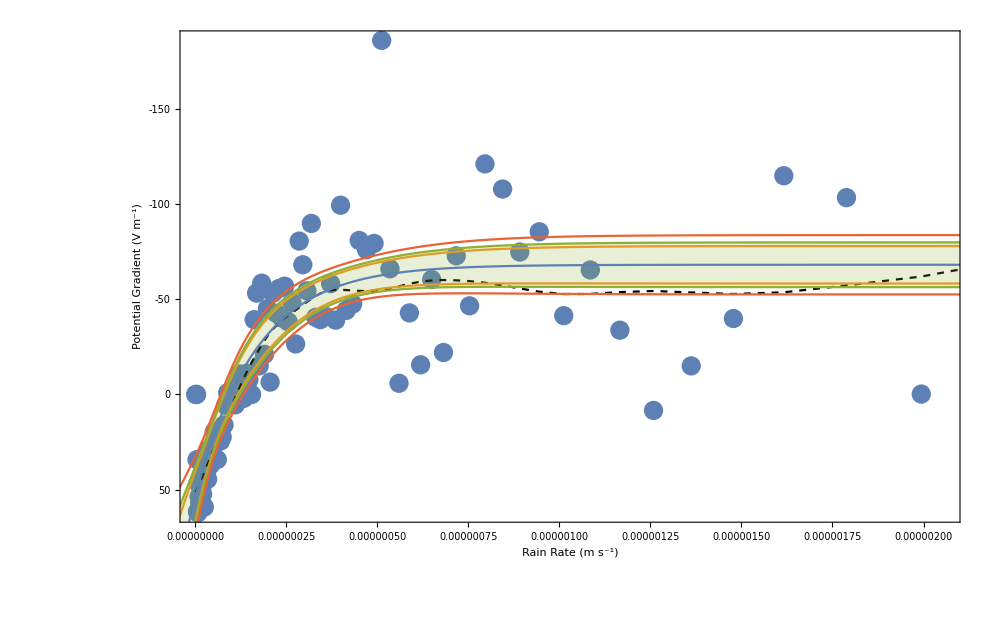

```mathematica
Show[ListPlot[PGEnsemble,PlotTheme->"Detailed",ImageSize->1000,FrameStyle->Large,FrameLabel->{"Rain Rate (m s^-1)", "Potential Gradient (V m^-1)", "Rain Rate"},FrameTicks->{{Automatic,Automatic},{Automatic,eVticks}}, ScalingFunctions->{Identity,"Reverse"}],ListLinePlot[PGLowess,ScalingFunctions->{Identity,"Reverse"}, PlotStyle->{Dashed, Black},PlotLegends->Placed[{"Lowess Local Weighted Smoothing"},{Right, Top}]],Plot[{PGEnsembleFit[x],bands90[x],bands95[x],bands99[x]},{x,-3*10^-6,3*10^-6},ScalingFunctions->{Identity,"Reverse"},PlotLegends->Placed[{"Quartic Polynomial"},{Right, Top}],Filling->{3->{1}}]]
```

```mathematica
PGData=PGData/.{0,___,___,___,___,___}:>Sequence[];
```

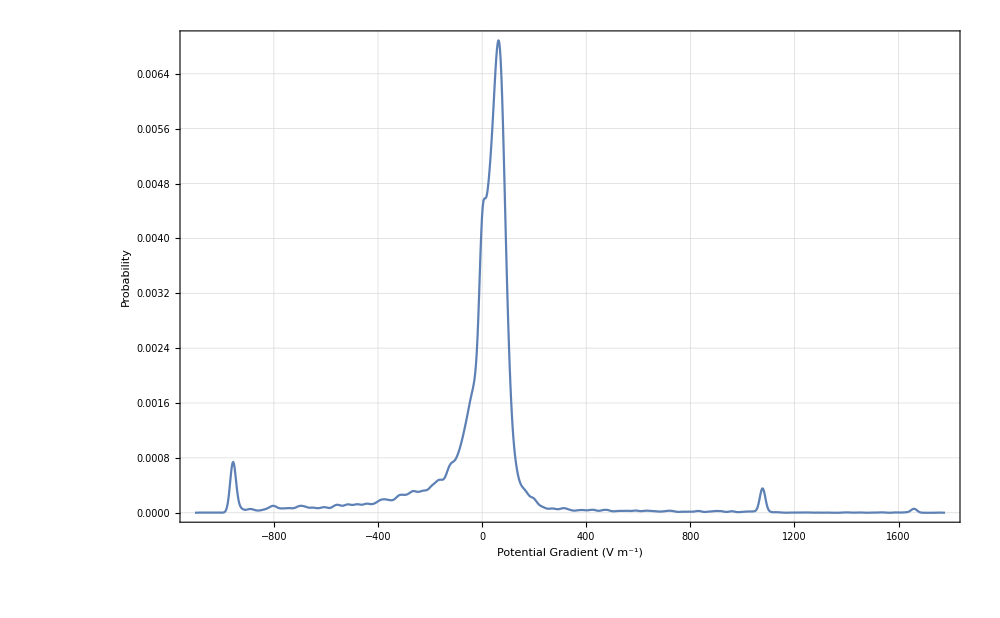

```mathematica
SmoothHistogram[PG,PlotRange->All, PlotTheme->"Detailed",ImageSize->1000, FrameLabel->{"Potential Gradient (V m^-1)", "Probability"}, FrameStyle->Large]
```

```mathematica
EstimatedDistribution[PG,NormalDistribution[a,b]]
```

NormalDistribution[-12.7608,273.817]

```mathematica
PDF[NormalDistribution[-12.760780611465835,273.81654186136007],x]
```

0.00145697 ⅇ^(-6.66885×10^-6 (12.7608+x)^2)

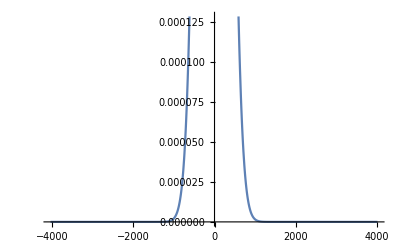

```mathematica
Plot[0.001456969245500978 ⅇ^(-6.668845280884606*^-6 (12.760780611465835+x)^2),{x,-4037.0256447740394,4011.5040835511077}]
```

```mathematica
MannWhitneyTest[PG,PDF[EstimatedDistribution[PG,NormalDistribution[a,b]]]]
```

MannWhitneyTest::rctndmln: The argument {145.436, 63.9676, -188.354, -110.568, -105.298, -43.6134, -69.4449, -113.203, -195.989, -169.099, -115.838, -58.905, -88.9482, -61.54, -191.259, -513.959, -542.425, -224.996, 78.7192, « 14 », 481.851, 77.1425, -159.348, -428.009, 156.775, 166.797, 485.803, 83.4708, 1077.44, 208.978, 64.7559, 72.9309, -83.6782, -388.991, -39.3801, -21.4536, 31.8078, « 15690 »} at position 1 should be a list containing two rectangular arrays of real numbers where each array has length greater than its dimension.

MannWhitneyTest[{145.436,63.9676,-188.354,-110.568,-105.298,-43.6134,-69.4449,-113.203,-195.989,-169.099,-115.838,-58.905,-88.9482,-61.54,-191.259,-513.959,-542.425,15706,-227.631,8.58963,1101.16,210.555,-750.719,100.339,97.1857,76.0842,27.5745,965.112,-354.197,19.1512,-941.605,37.0778,61.3326,-295.125,-952.145},1&]
 |  |  |  |

```mathematica
PGEnsembleFit["DesignMatrix"]
```

44.7532-90.134 DesignMatrix+74.2584 DesignMatrix^2-20.0779 DesignMatrix^3+1.79587 DesignMatrix^4

```mathematica
PGEnsembleFit["CorrelationMatrix"]//MatrixForm
```

(1. | -0.852022 | 0.724185 | -0.637839 | 0.57577
-0.852022 | 1. | -0.966572 | 0.912988 | -0.861263
0.724185 | -0.966572 | 1. | -0.985601 | 0.957299
-0.637839 | 0.912988 | -0.985601 | 1. | -0.992012
0.57577 | -0.861263 | 0.957299 | -0.992012 | 1.)

```mathematica
PGEnsembleFit["AdjustedRSquared"]
```

0.924257

```mathematica
PGEnsembleFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 44.7532 | 5.12116 | 8.73889 | 8.17013×10^-14
b | -90.134 | 14.4885 | -6.22106 | 1.32174×10^-8
c | 74.2584 | 11.9894 | 6.19367 | 1.49609×10^-8
d | -20.0779 | 3.64795 | -5.50388 | 3.14445×10^-7
e | 1.79587 | 0.365537 | 4.91296 | 3.73338×10^-6

```mathematica
Select[PGData[[All,4]],#<5&]
```

{0,0,0,0,0,0.0696524,0.297133,0.64288,0.622278,0.865426,1.06383,0.909091,0.922935,1.58983,1.19403,1.25156,0.999001,0.62383,0.709471,0.852878,0.856164,1.07933,2.02224,1.29282,1.13379,0.918695,1.10926,0.147907,0.0223644,0.0915919,0.387898,1.66389,0.13986,0.483209,2.90276,1.11607,2.51889,0.735294,1.02302,0.735294,1.05097,0.846382,1.41143,0.513479,2.71739,0.649984,1.52207,2.457,0.109975,0.0738007,0.829531,2.29885,2.3015,0.841043,0.491159,0.0325277,0.129634,0.363967,0.124587,0.19802,1.06383,0.590667,2.83286,1.67084,1.32363,2.30681,0.0110998,0,0.0166478,0.451671,0.146199,0.0874317,0.429092,0.61862,0.623441,0.677277,0.946074,1.03146,0.712251,0.809061,0.896459,0.349711,0.027337,0.0143598,0.528681,0.741565,0.306232,0.377786,0.596481,0.90212,1.15942,1.09951,0.961076,0.739372,0.781555,0.75815,0.4004,0.59952,0.555556,0.0122206,0.191589,0,0.0272324,1.37174,3.91389,0.0230216,0,0.0142795,0.655308,0.435256,0.155678,0.549149,0.0653189,0.0803955,0.482859,2.54453,1.33333,1.35318,1.443,1.86567,1.85529,1.47275,1.28783,1.11982,0.66778,0.356633,0.604961,0.730994,0.790514,1.52207,1.79533,1.83655,1.44823,1.42045,0.718649,1.17855,0.4363,0.905797,0.0445325,0.881057,0.764526,0.0420734,0.279057,1.30463,1.11607,0.558503,0.195446,0.417188,0.83612,1.38696,2.40096,1.06838,1.96078,2.35294,1.62602,3.78788,4.04858,2.60078,4.55581,4.47427,2.61097,2.00401,1.15207,1.50602,0.777605,2.51889,1.54799,1.25235,0.832293,0.325045,1.1396,1.17233,1.37646,1.18624,0.637146,0.356443,0.0480607,0.0122857,0,0}

```mathematica
RainRateBoundary =Select[PGData[[All,4]],#<1&];
```

```mathematica
RainRateBoundaryDist = SmoothKernelDistribution[RainRateBoundary]
```

DataDistribution[…]

```mathematica
FindMaximum[PDF[RainRateBoundaryDist,x],{x,0.1}, MaxIterations->100]
```

{1.12587,{x→0.0557204}}

```mathematica
RainRateBoundaryValue=FindMaximum[PDF[RainRateBoundaryDist,x],{x,0.1}, MaxIterations->100]
```

{1.12587,{x→0.0557204}}

```mathematica
0.2/RainRateBoundaryValue[[2,1,2]]
```

3.58935

```mathematica
p1=SmoothHistogram[RainRateBoundary, PlotTheme->"Scientific", ImageSize->Medium, FrameLabel->{"Rain Rate (mm yr^-1)","Density","Rain Rate Boundary"}, FrameStyle->Medium, GridLines->{{RainRateBoundaryValue[[2,1,2]]},{}}];
```

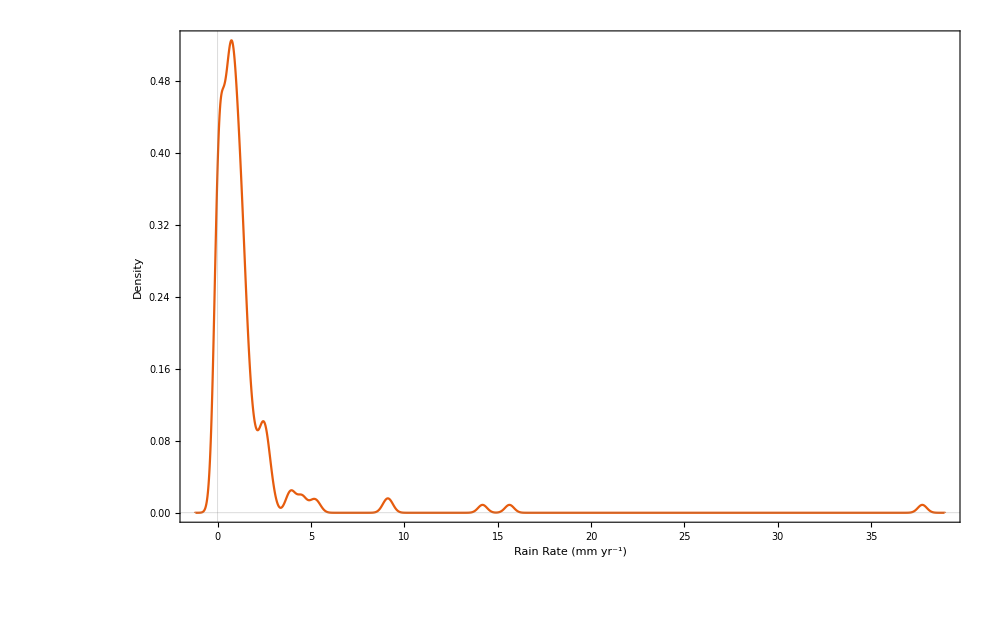

```mathematica
SmoothHistogram[PGData[[All,4]], PlotTheme->"Scientific", ImageSize->1000, FrameLabel->{"Rain Rate (mm yr^-1)","Density","Kernal Density Estimation"}, FrameStyle->Large, PlotRange->All, Epilog->Inset[p1,{30,0.4}]]
```

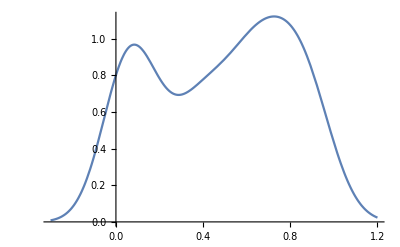

```mathematica
Plot[PDF[%186,x],{x,-0.3,1.2}]
```

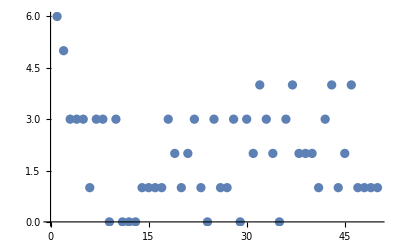

```mathematica
ListPlot[{6,5,3,3,3,1,3,3,0,3,0,0,0,1,1,1,1,3,2,1,2,3,1,0,3,1,1,3,0,3,2,4,3,2,0,3,4,2,2,2,1,3,4,1,2,4,1,1,1,1}]
```

```mathematica
{bins,heights}=HistogramList[RainRateBoundary,100];
```